## 1D System to solve with time dependence.

```mathematica
f={t,x}↦t+x
DSolve[{x'[t]==f[x[t],t],x[0]==x0}]
solution={t0,x0}↦x↦(Exp[-t0](1+t0+x0)) Exp[x]-x-1
```

Function[{t,x},t+x]

{{x[t]→-1+ⅇ^t-t+ⅇ^t x0}}

Function[{t0,x0},Function[x,(Exp[-t0] (1+t0+x0)) Exp[x]-x-1]]

## Solves with Euler Method

```mathematica
eulerForward={f,h}↦Apply[{t,x}↦{t+h,x+h f[t,x]}]
```

Function[{f,h},Apply[Function[{t,x},{t+h,x+h f[t,x]}]]]

```mathematica
step=eulerForward[f,0.1]
```

Apply[Function[{t$,x$},{t$+0.1,x$+0.1 Function[{t,x},t+x][t$,x$]}]]

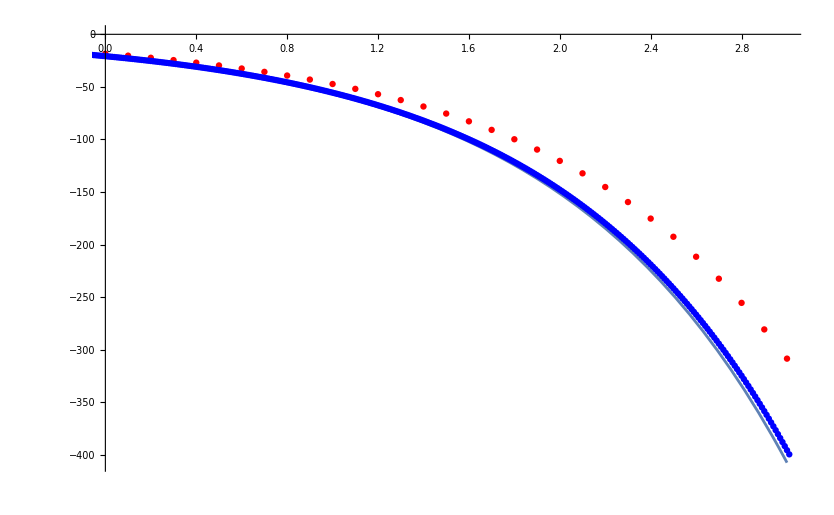

```mathematica
NestWhileList[eulerForward[f,0.1],{-3,1},#⟦1⟧<=3&];
NestWhileList[eulerForward[f,0.01],{-3,1},#⟦1⟧<=3&];
Show[
Plot[solution[-3,1][t],{t,0,3}],
ListPlot[{%%,%},PlotStyle->{Red,Blue},PlotRange->Full]
]
```

## Runge Kutta and RK-Fehlberg Method definitions

```mathematica
vectorise=f↦{t,x}↦f[t,Sequence@@x]
```

Function[f,Function[{t,x},f[t,Sequence@@x]]]

```mathematica
rk4={f,h}↦Apply[{t,x}↦Module[
{fV=vectorise[f],f0,f1,f2,f3},
f0=fV[t,x];
f1=fV[t+h/2,x+h/2 f0];
f2=fV[t+h/2,x+h/2 f1];
f3=fV[t+h,x+h f2];
{t+h,x+h/6(f0+2f1+2f2+f3)}
]];
```

```mathematica
β={{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}};
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
rkf45={f,tol}↦Module[{
stepPrime=rkf45prime[vectorise[f],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
];
```

## Comparisons of time evolution

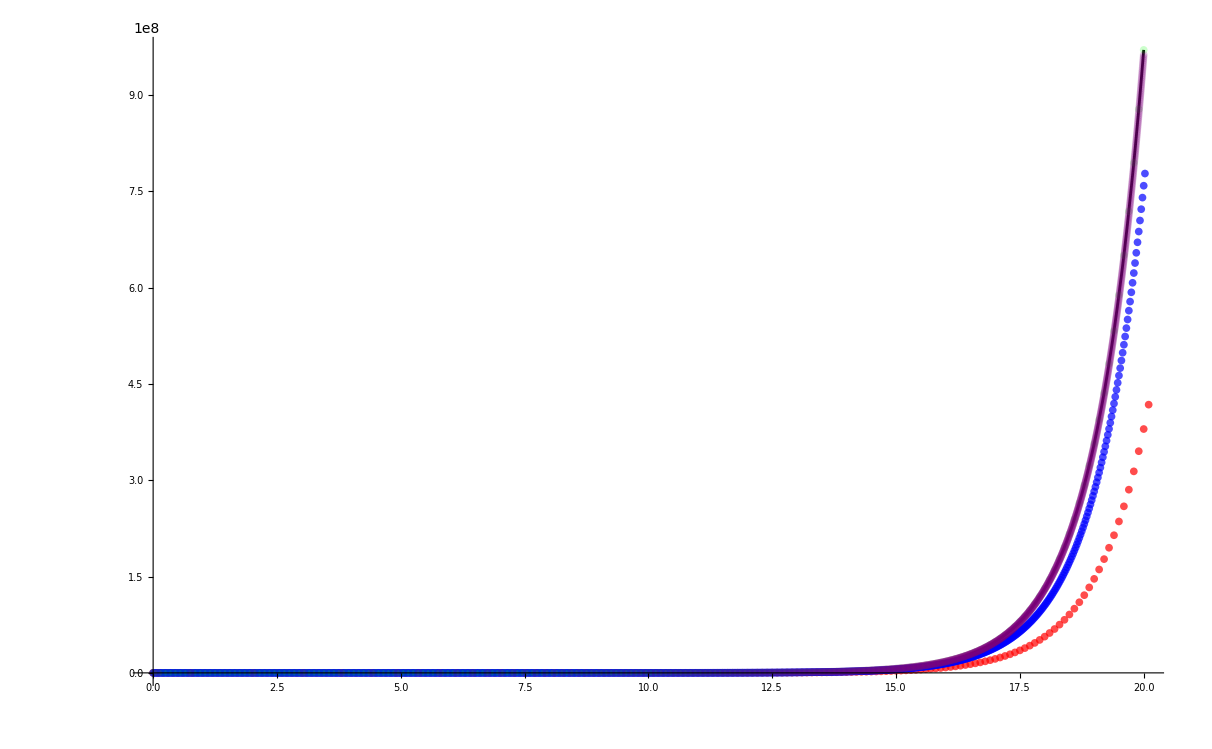

```mathematica
tMax=20;
NestWhileList[eulerForward[f,0.1],{0,1},#⟦1⟧<=tMax&];
NestWhileList[eulerForward[f,0.1/4],{0,1},#⟦1⟧<=tMax&];
NestWhileList[rk4[f,0.1],{0,1},#⟦1⟧<=tMax&];
Map[Take[#,2]&]@NestWhileList[rkf45[f,0.1],{0,1,0.1},#⟦1⟧<=tMax&];
Show[
Plot[solution[0,1][t],{t,0,tMax},PlotRange->Full,PlotStyle->Black],
ListPlot[{%%%%,%%%,%%,%},PlotStyle->{{Opacity[0.7],Red},{Opacity[0.7],Blue},{Opacity[0.2],Green},{Opacity[0.2],Purple}}]
]
```